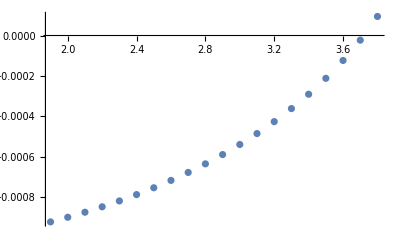

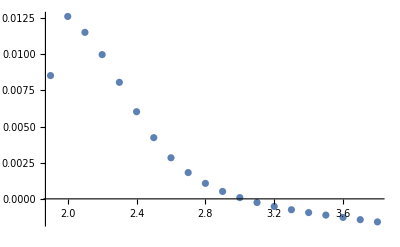

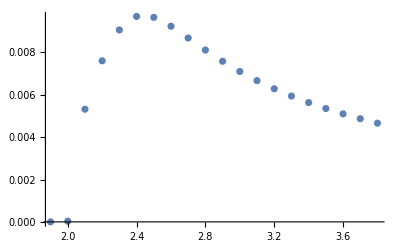

```mathematica
SetDirectory["/Users/alessandrobaroni/Dropbox/rho_FF/code_development/G_v2_cpp"];
SmoothIntegrandPlot=Import["int3dreal_Ecm.txt","Table"];
Smooth2DPlot=Import["int1dreal_Ecm.txt","Table"];
Smooth2DPlotI=Import["int1dimag_Ecm.txt","Table"];
ListPlot[SmoothIntegrandPlot]
ListPlot[Smooth2DPlot]
ListPlot[Smooth2DPlotI]
```

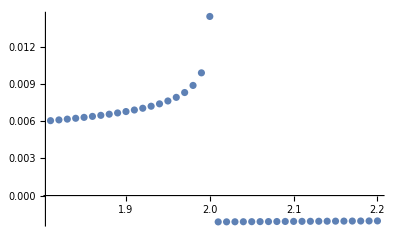

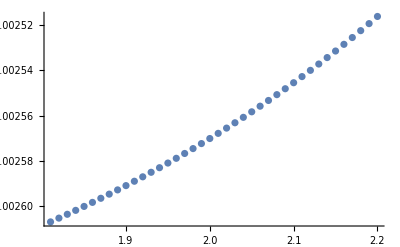

```mathematica
SetDirectory["/Users/alessandrobaroni/Dropbox/rho_FF/code_development/G_v2_cpp"];
Smooth2DPlot=Import["G_realsmooth3D_Ecm.txt","Table"];
ListPlot[Smooth2DPlot]
```

```mathematica
Clear[GRealEcm]
SetDirectory["/Users/abaroni/Desktop/G_v0i_cpp"]
(*dataAllReal=Import["G_values.txt","Table"][[All,{1,2,3}]];*)
(*GReal=Import["G_real3D_v1.txt","Table"];*)
GImagEcm=Import["G_imag3D_Ecm_v1.txt","Table"];
GRealEcm=Import["G_real3D_Ecm_v1.txt","Table"];
(*ListPlot3D[dataAllReal]*)
(*ListPlot3D[GReal,Ticks->None,Mesh->None,PlotStyle->Orange,InterpolationOrder->4,ClippingStyle->None]*)
ListPlot3D[GRealEcm,Mesh->None,PlotStyle->Orange,ClippingStyle->None,FillingStyle->Automatic,Lighting->"Neutral",Ticks->{Automatic,Automatic,None}]
ListPlot3D[GImagEcm,Mesh->None,PlotStyle->Orange,Ticks->{Automatic,Automatic,None},ClippingStyle->None,FillingStyle->Automatic,Boxed->True,Lighting->"Neutral"]
```

/Users/abaroni/Desktop/G_v0i_cpp

-Graphics3D-

-Graphics3D-

```mathematica
Export["testReG",%205,"PDF"]
```

testReG

```mathematica
Show[%190,Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
Show[%190,Lighting->Automatic]
```

-Graphics3D-

```mathematica
Show[%132,Ticks->{Automatic,Automatic,None}]
```

-Graphics3D-

```mathematica
Show[%134,Lighting->"Neutral",FillingStyle->Automatic]
```

-Graphics3D-

```mathematica
Show[%134,ViewPoint->{1.3,-2.4,2.}]
```

-Graphics3D-

```mathematica
Show[%124,Ticks->{Automatic,Automatic,None}]
```

-Graphics3D-

```mathematica
Show[%125,Background->None]
```

-Graphics3D-

```mathematica
Show[%125,ViewPoint->{1.3,-2.4,2.}]
```

-Graphics3D-

```mathematica
Show[%116,Ticks->{Automatic,Automatic,None}]
```

-Graphics3D-

-Graphics3D-

```mathematica
ListPlot3D[GRealEcm,Mesh->None,Mesh->None,PlotStyle->Orange,ClippingStyle->None,Ticks->None]
```

-Graphics3D-

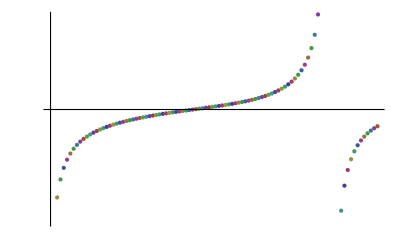

```mathematica
Show[%92,Ticks->None]
```